```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=(*√(m^2+p^2)*)p^2/(2m);Nx=25;max=100;
```

```mathematica
m =50/2;λ=π/2;
```

```mathematica
Clear@α
```

```mathematica
α=(*0.33375*)0.23310139229777338;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_][p_?NumberQ]:=ω[p]ϕ[n][p]-λ/π NIntegrate[(ϕ[n][k]-ϕ[n][p]-(k-p)ϕ[n]'[p])/(p-k)^2,{k,0,max}]
```

```mathematica
H1[n_][p_?NumberQ]:=ω[p]ϕ[n][p]
H2[n_][p_?NumberQ]:=-λ/π NIntegrate[(ϕ[n][k]-ϕ[n][p]-(k-p)ϕ[n]'[p])/(p-k)^2,{k,-max,0,max}]
```

```mathematica
ParallelTable[If[Abs[i-n]≤1,NIntegrate[ϕ[2i][p]H1[2n][p],{p,-max,max},MaxRecursion->10],0]+2NIntegrate[ϕ[2i][p]H2[2n][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {18.6516}. NIntegrate obtained -0.00144075 and 3.66541×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {22.6555}. NIntegrate obtained -0.00329041 and 7.20279×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {19.6281}. NIntegrate obtained -0.00126821 and 2.92804×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {14.9406}. NIntegrate obtained -0.000937764 and 1.2286×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {21.7766}. NIntegrate obtained -0.00266375 and 7.28255×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {19.6281}. NIntegrate obtained -0.00622309 and 7.98305×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {17.5773}. NIntegrate obtained -0.00112757 and 1.76805×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {22.8508}. NIntegrate obtained -0.00220931 and 4.33502×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {15.0383}. NIntegrate obtained -0.000881336 and 1.85677×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {20.2141}. NIntegrate obtained -0.00465741 and 3.6907×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {13.3781}. NIntegrate obtained -0.000830498 and 1.41985×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {22.1672}. NIntegrate obtained -0.00363368 and 1.24913×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {21.7766}. NIntegrate obtained -0.0265048 and 7.01984×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {21.2883}. NIntegrate obtained -0.0149718 and 2.88958×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {17.2844}. NIntegrate obtained -0.00968758 and 7.54695×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {21.1906}. NIntegrate obtained -0.00117579 and 1.30211×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {21.1906}. NIntegrate obtained -0.00136389 and 2.50552×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {22.2648}. NIntegrate obtained -0.00160661 and 3.33683×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {20.7023}. NIntegrate obtained -0.067548 and 1.04892×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {21.5813}. NIntegrate obtained -0.000785114 and 2.44789×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {21.5813}. NIntegrate obtained -0.000632616 and 2.59489×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {21.5813}. NIntegrate obtained -0.000625843 and 4.02561×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {23.0461}. NIntegrate obtained -0.028925 and 2.9761×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {27.5383}. NIntegrate obtained -0.0164098 and 7.91839×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{20025.1,{{0.385615,0.107112,-0.0421757,-0.0230965,-0.015432,-0.0113867,-0.00891976,-0.00727294,-0.00610306,-0.00523333,-0.00456389,-0.0040343,-0.00360594,-0.00325304,-0.0029578,-0.00270752,-0.00249296,-0.00230717,-0.00214491,-0.00200209,-0.00187553,-0.00176267,-0.001661,-0.00156976,-0.00148785,-0.00141098},{0.121267,1.43162,0.411435,-0.0490244,-0.0240066,-0.014953,-0.010512,-0.00794788,-0.00630729,-0.00518074,-0.00436616,-0.00375353,-0.00327829,-0.00290031,-0.00259343,-0.00233995,-0.0021275,-0.00194717,-0.00179243,-0.00165844,-0.00154121,-0.00143824,-0.00134295,-0.00125786,-0.00119484,-0.00110124},{-0.0421606,0.446151,2.34852,0.721219,-0.0573946,-0.0268958,-0.0162132,-0.0111119,-0.00823262,-0.00642593,-0.00520601,-0.00433675,-0.00369136,-0.00319638,-0.00280669,-0.00249316,-0.00223631,-0.00202263,-0.00184241,-0.00168929,-0.00155609,-0.00144236,-0.00131591,-0.00122679,-0.00120652,-0.000974525},{-0.0230964,-0.0489656,0.776178,3.22668,1.03766,-0.0650379,-0.029776,-0.017618,-0.0118893,-0.00869473,-0.00671187,-0.00538605,-0.00444969,-0.00376006,-0.00323503,-0.00282441,-0.0024961,-0.0022287,-0.00200697,-0.0018235,-0.00166237,-0.00153047,-0.00132962,-0.00118807,-0.00146589,-0.00071476},{-0.0154319,-0.0240064,-0.057267,1.11284,4.08386,1.3588,-0.0720011,-0.0324908,-0.0189963,-0.0126878,-0.0091956,-0.00704277,-0.0056124,-0.00460811,-0.00387249,-0.00331525,-0.0028815,-0.00253641,-0.00225515,-0.00202945,-0.00182787,-0.00166751,-0.00156596,-0.000943936,-0.0014537,-0.000288451},{-0.0113867,-0.014953,-0.0268951,-0.064816,1.45423,4.92733,1.68337,-0.0784174,-0.0350358,-0.0203159,-0.0134699,-0.00969875,-0.00738464,-0.00585384,-0.00478348,-0.00400251,-0.00341306,-0.00295631,-0.00259117,-0.00230677,-0.00205541,-0.00184025,-0.00166852,-0.00124776,-0.00194261,-0.000390377},{-0.00891976,-0.010512,-0.0162132,-0.0297746,-0.0716589,1.79908,5.7609,2.01058,-0.0843945,-0.0374296,-0.0215734,-0.0142258,-0.0101922,-0.0077253,-0.00609861,-0.0049647,-0.00413969,-0.00351946,-0.00303541,-0.00266531,-0.00235395,-0.00195446,-0.00187712,-0.0014515,-0.0023455,-0.00018872},{-0.00727294,-0.00794788,-0.0111119,-0.017618,-0.0324881,-0.0779285,2.14662,6.58691,2.33988,-0.0900132,-0.0396922,-0.0227727,-0.0149534,-0.0106719,-0.00805989,-0.00634172,-0.00514674,-0.00427991,-0.00362583,-0.00312928,-0.0027255,-0.00230059,-0.00246508,-0.00155944,-0.00331358,0.000753878},{-0.00610306,-0.00630729,-0.00823262,-0.0118893,-0.0189962,-0.0350315,-0.0837322,2.4963,7.40689,2.67089,-0.0953339,-0.0418411,-0.0239189,-0.0156535,-0.0111367,-0.00838654,-0.00658082,-0.00532751,-0.00441861,-0.00373626,-0.00321312,-0.00269898,-0.00297836,-0.00138976,-0.0039022,-6.42425×10^-6},{-0.00523333,-0.00518074,-0.00642593,-0.00869473,-0.0126878,-0.0203158,-0.037423,-0.0891504,2.84775,8.22191,3.00334,-0.100403,-0.0438909,-0.0250174,-0.016328,-0.0115869,-0.00870461,-0.00681479,-0.00550601,-0.00455398,-0.0038204,-0.00307832,-0.00333686,-0.00235717,-0.00390818,-0.000355985},{-0.00456389,-0.00436616,-0.00520601,-0.00671187,-0.0091956,-0.0134699,-0.0215734,-0.0396826,-0.0942433,3.20068,9.03276,3.33701,-0.105257,-0.0458535,-0.026073,-0.0169787,-0.0120231,-0.00901394,-0.0070439,-0.00567538,-0.00465986,-0.00364723,-0.00339301,-0.00302432,-0.00281704,-0.000716605},{-0.0040343,-0.00375353,-0.00433675,-0.00538605,-0.00704277,-0.00969875,-0.0142258,-0.0227725,-0.0418277,-0.099057,3.55487,9.84004,3.67173,-0.109925,-0.047739,-0.02709,-0.0176076,-0.0124462,-0.00931483,-0.00726737,-0.00595106,-0.00494639,-0.00415048,-0.0030843,-0.00318016,0.000557893},{-0.00360594,-0.00327829,-0.00369136,-0.00444969,-0.0056124,-0.00738464,-0.0101922,-0.0149534,-0.0239186,-0.0438727,-0.103627,3.91018,10.6442,4.00737,-0.114431,-0.0495557,-0.028072,-0.0182167,-0.0128563,-0.00960844,-0.00752101,-0.00635353,-0.00497722,-0.00440191,-0.00356417,0.00042461},{-0.00325304,-0.00290031,-0.00319639,-0.00376006,-0.00460812,-0.00585384,-0.00772529,-0.0106719,-0.0156535,-0.025017,-0.0458295,-0.107983,4.26646,11.4457,4.34383,-0.118793,-0.0513106,-0.0290221,-0.0188074,-0.0132555,-0.00993853,-0.00809969,-0.0063149,-0.00516933,-0.0044184,-0.00353369},{-0.0029578,-0.00259343,-0.00280668,-0.00323503,-0.00387249,-0.00478348,-0.00609862,-0.0080599,-0.0111367,-0.016328,-0.0260725,-0.047708,-0.112146,4.6236,12.2447,4.681,-0.123027,-0.0530097,-0.0299437,-0.0193752,-0.013643,-0.0100188,-0.00795019,-0.00635474,-0.00507171,-0.00457167},{-0.00270752,-0.00233995,-0.00249316,-0.00282442,-0.00331525,-0.0040025,-0.00496469,-0.00634171,-0.00838654,-0.0115869,-0.0169787,-0.0270893,-0.0495165,-0.116137,4.98153,13.0415,5.01883,-0.127149,-0.0546575,-0.0308384,-0.0199359,-0.0136779,-0.0105981,-0.00836206,-0.00697469,-0.00651411},{-0.00249296,-0.0021275,-0.00223631,-0.0024961,-0.00288152,-0.00341309,-0.00413973,-0.00514677,-0.00658084,-0.00870461,-0.0120231,-0.0176076,-0.0280711,-0.0512618,-0.119971,5.34016,13.8364,5.35724,-0.131168,-0.0562605,-0.0317075,-0.0205899,-0.0142056,-0.0113952,-0.00839668,-0.00663937},{-0.00230717,-0.00194717,-0.00202262,-0.00222864,-0.00253622,-0.00295589,-0.00351885,-0.00427938,-0.00532734,-0.00681502,-0.00901407,-0.012446,-0.0182166,-0.0290211,-0.0529497,-0.123661,5.69943,14.6295,5.69619,-0.135096,-0.05785,-0.0328195,-0.0208061,-0.0138042,-0.0110752,-0.00749412},{-0.00214491,-0.00179244,-0.00184247,-0.00200729,-0.00225609,-0.00259311,-0.00303851,-0.00362797,-0.00441905,-0.00550521,-0.00704385,-0.00931518,-0.0128566,-0.018807,-0.029942,-0.0545853,-0.127219,6.05929,15.421,6.03562,-0.138943,-0.0592755,-0.0335176,-0.0207287,-0.0153099,-0.0118832},{-0.00200209,-0.00165838,-0.00168884,-0.00182158,-0.00202513,-0.00229969,-0.00265832,-0.00312505,-0.0037381,-0.00455749,-0.00567982,-0.00726729,-0.00960832,-0.0132557,-0.0193806,-0.0308362,-0.0561728,-0.130654,6.4197,16.211,6.37552,-0.142252,-0.0609811,-0.03545,-0.0214609,-0.0149508},{-0.00187553,-0.00154126,-0.00155649,-0.00166391,-0.00183206,-0.0020585,-0.00235158,-0.00272778,-0.00321323,-0.00384794,-0.004694,-0.00585091,-0.00748544,-0.0098939,-0.013644,-0.0199384,-0.0317059,-0.057716,-0.133975,6.7806,16.9996,6.71572,-0.146272,-0.0626778,-0.0361244,-0.0204581},{-0.00176267,-0.00143815,-0.00144145,-0.00152863,-0.00166865,-0.00185738,-0.00209998,-0.00240792,-0.0027994,-0.0033019,-0.00395685,-0.00482828,-0.0060184,-0.00769842,-0.0101723,-0.0140224,-0.0204817,-0.0325529,-0.0592179,-0.137187,7.14197,17.7867,7.05656,-0.149064,-0.0642222,-0.0368053},{-0.00166149,-0.00134678,-0.00134069,-0.00141157,-0.00152903,-0.00168778,-0.00189072,-0.00214587,-0.00246628,-0.00287147,-0.00338996,-0.00406431,-0.00496026,-0.00618247,-0.00790661,-0.0104441,-0.0143914,-0.0210117,-0.0333786,-0.0606823,-0.140276,7.50412,18.5729,7.39778,-0.152057,-0.0685716},{-0.00157023,-0.00126523,-0.00125169,-0.00130917,-0.00140816,-0.00154277,-0.00171452,-0.00192892,-0.00219524,-0.00252697,-0.00294447,-0.0034773,-0.00416967,-0.00508933,-0.0063426,-0.0081102,-0.0107093,-0.0147514,-0.021529,-0.0341852,-0.0621098,-0.143245,7.86616,19.3568,7.73924,-0.155354},{-0.00148789,-0.00119243,-0.00117311,-0.00121988,-0.00130395,-0.00141858,-0.00156385,-0.00174396,-0.00196648,-0.00224251,-0.00258588,-0.00301682,-0.00356471,-0.00427525,-0.00521748,-0.00650059,-0.00830937,-0.0109691,-0.0151038,-0.022034,-0.0350071,-0.0639189,-0.146084,8.22903,20.1405,8.08182},{-0.00141216,-0.00112586,-0.00110147,-0.00113862,-0.00120975,-0.001309,-0.00143643,-0.00159426,-0.00178512,-0.00201546,-0.00229777,-0.00264669,-0.00308601,-0.00364762,-0.00437396,-0.00533887,-0.00665371,-0.00850371,-0.0112217,-0.0154468,-0.0225031,-0.0356454,-0.064969,-0.147529,8.59226,20.9209}}}

{0.368736,1.1868,1.76382,2.25704,2.70113,3.11359,3.52072,3.97093,4.49901,5.11345,5.8139,6.60343,7.48284,8.45711,9.52894,10.7107,12.0036,13.4241,14.9811,16.6981,18.5938,20.7031,23.0823,25.7985,29.0361,33.0917}

```mathematica
ParallelTable[If[Abs[i-n]≤1,NIntegrate[ϕ[2i+1][p]H1[2n+1][p],{p,-max,max},MaxRecursion->10],0]+2NIntegrate[ϕ[2i+1][p]H2[2n+1][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

```mathematica
2NIntegrate[ϕ[30][p]H2[30][p],{p,0,200},MaxRecursion->10]//Timing
```

{70.7969,3.69674}

```mathematica
2NIntegrate[ϕ[30][p]H2[30][p],{p,0,max},MaxRecursion->10]//Timing
```

{62.9688,3.69674}

```mathematica
NIntegrate[ϕ[30][p]H2[30][p],{p,-max,max},MaxRecursion->10]//Timing
```

{109.688,3.69674}

```mathematica
NIntegrate[ϕ[30][p]H1[30][p],{p,-max,max},MaxRecursion->20]//Timing
```

{0.109375,2.71502}

```mathematica
NIntegrate[ϕ[10][p]H1[30][p],{p,-max,max},MaxRecursion->30]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.22839×10^-17 and 2.3871×10^-16 for the integral and error estimates.

{1.51563,4.22839×10^-17}

```mathematica
NIntegrate[ϕ[6][p]H1[10][p],{p,-max,max},MaxRecursion->30]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.26669×10^-17 and 4.9707×10^-17 for the integral and error estimates.

{1.125,-6.26669×10^-17}

```mathematica
With[{i=5,n=5},If[Abs[i-n]≤1,NIntegrate[ϕ[2i][p]H1[2n][p],{p,-max,max},MaxRecursion->10],0]]
```

0.934679

```mathematica
(ϕ[30][p]H[30][p]-ϕ[30][-p]H[30][-p])/.p->100
```

```mathematica
NIntegrate[ϕ[30][p]H[30][p],{p,-max,max},MaxRecursion->50]//Timing
```

{77.3281,28.2998}

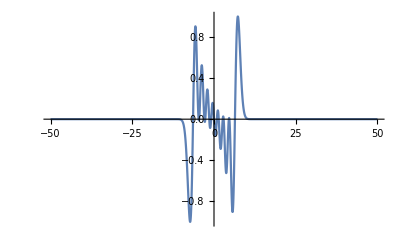

```mathematica
Plot[ϕ[6][p]H[9][p],{p,-50,50},PlotRange->All]
```

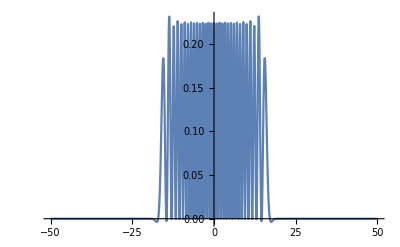

```mathematica
Plot[ϕ[30][p]H2[30][p],{p,-50,50},PlotRange->All]
```